## CriticalFamiliesSize4Tangent (Avoiding 3 disks in a slab)

## Tangent Critical F4, case (i), ℓ_def13L supports C4 on RHS, ℓ_sep23 supports C4 on left (from above)

0.690599

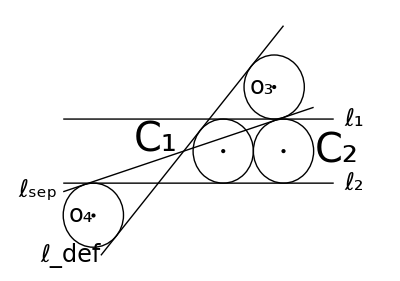

```mathematica
(*taken from: CriticalFamiliesSize4Overlapping *)(*Compare with Case A(i)*)
δ=r;
 (*magnitude of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;
k=(2r)/(3δ+γ+Sqrt[4 r^2+γ^2+2δ*γ+δ^2]);(*slope of line lsep for C2/C3*)
t=(2/3)r + δ; (*t must be in the bound δ+2r < t < 3δ *)(*center x-coordinate for C3*)
γ=N[r/3(9 - 4*Sqrt[3])](*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
Subscript[x, 4]=-(Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+γ+2δ);(*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];(*Three disks within horizontal slab between line Subscript[ℓ, 1] and line Subscript[ℓ, 2]*)
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{Subscript[x, 4]-r,r},{t+r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{Subscript[x, 4]-r,-r},{t+r,-r}}],(*Black,(*support line Subscript[m, 1], vertical*)Line[{{δ-r,-3(r)},{δ-r,3(r)}}],Black,(* support line Subscript[m, 3], vertical*)Line[{{δ+r,-(3r)},{δ+r,(3r)}}]*)}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r/2,r/3},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+2r+b/2,-2r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def]*)Line[{{Subscript[x, 4]+r/4,(2r)/(γ+δ)*(Subscript[x, 4]+r/4)+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)},{δ,(2r)/(γ+δ)*(δ)+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep]*)Line[{{Subscript[x, 4]-r,k*(Subscript[x, 4]-r)-k*(δ+γ)/2+r},{δ+r,k*(δ+r)-k*(δ+γ)/2+r}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, def],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+r/4,(2r)/(γ+δ)*(Subscript[x, 4]+r/4)+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, sep],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]-r-ε,k*(Subscript[x, 4]-r-ε)-k*δ/2+r},{1,0}]];
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,2r}],Point[{Subscript[x, 4],-2r}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,2r},r],(*Disk C4 *)Circle[{Subscript[x, 4],-2r},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,2r},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],-2r},{1,0}]];
g22=Graphics[Text[
Style[Subscript[ℓ, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{t+r+2b,r},{1,0}]];
g23=Graphics[Text[
Style[Subscript[ℓ, 2],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{t+r+2b,-r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangenti *)(*see handwritten pages for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21,g22,g23]
```

## Tangent Critical F4, case (ii), ℓ_def13L supports C4 on RHS, ℓ_sep supports C4 on right (from below)

0.295598

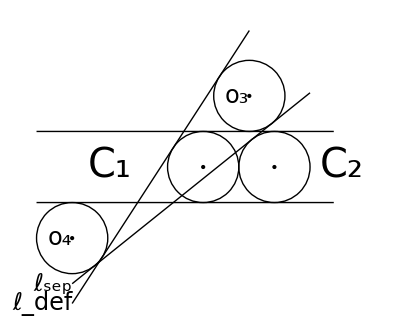

```mathematica
(*Originally from: Familyof5CirclesDisjointCorollary *)
(*taken from: SupportSkProperty3DisksCollinearNondisjont *)
(*δ=2/(√3);*)
δ=r;
 (*magnitude of x-coordinate of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;
k=(4r)/(2δ+2γ+√(4 r^2+γ^2+2δ*γ+δ^2));(*slope of line lsep for C2/C3*)
t=(2/3)r + δ; 
β=13+3Sqrt[33];γ=N[r/(3CubeRoot[β])*(CubeRoot[2*β^(2)]- CubeRoot[β]-4*CubeRoot[4])](*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
Subscript[x, 4]=-(Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+γ+2δ);(*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
(*Subscript[s, 2]=(2r)/(Sqrt[t+δ+2r]Sqrt[t+δ-2r]);*) (*This is the slope of Subscript[m, 2](x), hence the mnemonic.*)
(*Subscript[s, 3]=(2r)/(Sqrt[t-δ+2r]Sqrt[t-δ-2r]);*) (*This is the slope of Subscript[m, 3](x), hence the mnemonic.*)
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];(*Three disks within horizontal slab between line Subscript[ℓ, 1] and line Subscript[ℓ, 2]*)
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{Subscript[x, 4]-r,r},{t+r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{Subscript[x, 4]-r,-r},{t+r,-r}}],(*Black,(*support line Subscript[m, 1], vertical*)Line[{{δ-r,-3(r)},{δ-r,3(r)}}],Black,(* support line Subscript[m, 3], vertical*)Line[{{δ+r,-(3r)},{δ+r,(3r)}}]*)}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r,0},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+(3r)/2,-3r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def]*)Line[{{Subscript[x, 4],(2r)/(γ+δ)*(Subscript[x, 4])+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)},{γ,(2r)/(γ+δ)*(γ)+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep]*)Line[{{Subscript[x, 4],k*(Subscript[x, 4])-k*(δ+γ)/2+r},{δ+r,k*(δ+r)-k*(δ+γ)/2+r}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, def],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],(2r)/(γ+δ)*(Subscript[x, 4])+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, sep],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],k*(Subscript[x, 4])-k*(δ+γ)/2+r},{1,0}]];(*{Subscript[x, 4]-r-ε,k*(Subscript[x, 4]-r-ε)-k*δ/2+r}*)
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,2r}],Point[{Subscript[x, 4],-2r}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,2r},r],(*Disk C4 *)Circle[{Subscript[x, 4],-2r},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,2r},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],-2r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentii *)(*see handwritten pages 11/20/19 for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21]
```

## Tangent Critical F4, case (iii), ℓ_def13L supports C4 on RHS, ℓ_def23R supports C4 on left (from below)

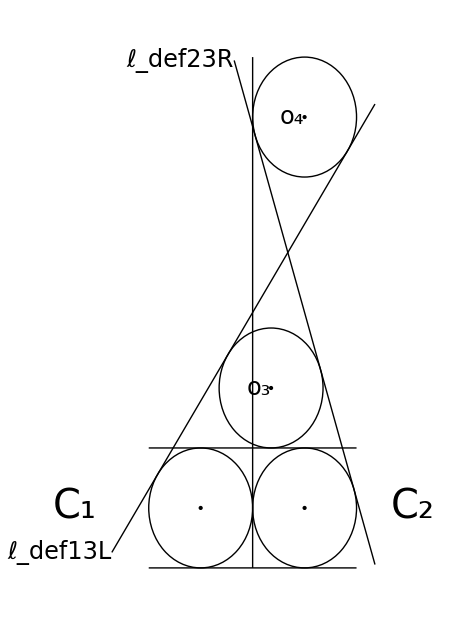

```mathematica
(*Copied from Case (ii) above *)
δ=r;
 (*magnitude of x-coordinate of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ldef23Rslope=(-2r)/(δ-γ);(*slope of line Subscript[ℓ, def23R] for C2/C3*)
ldef23Rint=(2r*δ+r*Sqrt[4 r^2+δ^2-2δ*γ+γ^2])/(r-γ);
t=(2/3)r + δ; 
γ=0.3551287987727411 (*2.392030791355326*);
(*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
Subscript[y, 4]=(2r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+4 r^2)/(γ+r);(*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
Subscript[x, 4]=r;
(*Subscript[s, 2]=(2r)/(Sqrt[t+δ+2r]Sqrt[t+δ-2r]);*) (*This is the slope of Subscript[m, 2](x), hence the mnemonic.*)
(*Subscript[s, 3]=(2r)/(Sqrt[t-δ+2r]Sqrt[t-δ-2r]);*) (*This is the slope of Subscript[m, 3](x), hence the mnemonic.*)
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];(*Two disks within horizontal slab between line Subscript[ℓ, 1] and line Subscript[ℓ, 2]*)
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{-r-r,r},{r+r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{-r-r,-r},{r+r,-r}}],Black,(*support line Subscript[ℓ, v], vertical*)Line[{{0,-(r)},{0,Subscript[y, 4]+r}}](*,Black,(* support line Subscript[m, 3], vertical*)Line[{{δ+r,-(3r)},{δ+r,(3r)}}]*)}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r,0},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+(3r)/2,-3r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def13L]*)Line[{{-2r-(r+γ-Abs[r-γ])/(r+γ+Abs[r-γ])-γ,(2r)/(γ+δ)*(-2r-(r+γ-Abs[r-γ])/(r+γ+Abs[r-γ])-γ)+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)},{Subscript[x, 4]+r+γ/r,(2r)/(γ+δ)*(Subscript[x, 4]+r+γ/r)+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, def23R]*)Line[{{-γ/r,ldef23Rslope*(-γ/r)+ldef23Rint},{δ+r+γ/r,ldef23Rslope*(δ+r+γ/r)+ldef23Rint}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, def13L],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2r-(r+γ-Abs[r-γ])/(r+γ+Abs[r-γ])-γ,(2r)/(γ+δ)*(-2r-(r+γ-Abs[r-γ])/(r+γ+Abs[r-γ])-γ)+(r*Sqrt[4 r^2+γ^2+2δ*γ+δ^2]+2r*δ)/(γ+δ)},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, def23R],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-γ/r,ldef23Rslope*(-γ/r)+ldef23Rint},{1,0}]];(*{Subscript[x, 4]-r-ε,k*(Subscript[x, 4]-r-ε)-k*δ/2+r}*)
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,2r}],Point[{Subscript[x, 4],Subscript[y, 4]}],PointSize[0.05]}];
g18=Graphics[{(*Disk C3*)Circle[{γ,2r},r],(*Disk C4 *)Circle[{r,Subscript[y, 4]},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,2r},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],Subscript[y, 4]},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentiii *)(*see handwritten pages 11/20/19 for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21]
```

## The determining equation of the family case (iii)

```mathematica
Clear[r,γ]
(2r+Sqrt[5*r^{2}+2r*γ+ γ^{2}])/(γ+r)= Sqrt[4r^{2}+(r-γ)^{2}]/(r-γ)
```

Set::write: Tag Plus in (4 r (r-γ))/(r+γ)+{((r-3 γ) √(5 r^2+2 r γ+γ^2))/(r+γ)} is Protected.

{√(4 r^2+(r-γ)^2)}

```mathematica
(*Collect,Expand,ExpandAll,Solve,Simplify,Together,PowerExpand,Cancel*)
Clear[r,γ]
Simplify[MultiplySides[(2r+Sqrt[5*r^{2}+2r*γ+ γ^{2}])/(γ+r)== Sqrt[4r^{2}+(r-γ)^{2}]/(r-γ),γ+r]]
```

Piecewise[{{{2 r+√(5 r^2+2 r γ+γ^2)}=={(√(4 r^2+(r-γ)^2) (r+γ))/(r-γ)}, r+γ≠0}, {{(2 r+√(5 r^2+2 r γ+γ^2))/(r+γ)}=={(√(4 r^2+(r-γ)^2))/(r-γ)}, True}}]

```mathematica
Simplify[MultiplySides[2 r+√(5 r^2+2 r γ+γ^2)==(√(4 r^2+(r-γ)^2) (r+γ))/(r-γ),r-γ]]
```

Piecewise[{{(r-γ) (2 r+√(5 r^2+2 r γ+γ^2))==(r+γ) √(5 r^2-2 r γ+γ^2), r≠γ}, {2 r+√(5 r^2+2 r γ+γ^2)==((r+γ) √(5 r^2-2 r γ+γ^2))/(r-γ), True}}]

### Revised approach to equation

```mathematica
Clear[r,γ]
MultiplySides[(2r+Sqrt[5*r^{2}+2r*γ+ γ^{2}])/(γ+r)== Sqrt[4r^{2}+(r-γ)^{2}]/(r-γ),(γ+r)*(r-γ)]
```

Piecewise[{{{(r-γ) (2 r+√(5 r^2+2 r γ+γ^2))}=={√(4 r^2+(r-γ)^2) (r+γ)}, (r-γ) (r+γ)≠0}, {{(2 r+√(5 r^2+2 r γ+γ^2))/(r+γ)}=={(√(4 r^2+(r-γ)^2))/(r-γ)}, True}}]

```mathematica
Expand[((r-γ) (2 r+√(5 r^2+2 r γ+γ^2)))^2==(√(4 r^2+(r-γ)^2) (r+γ))^2]
```

9 r^4-16 r^3 γ+6 r^2 γ^2+γ^4+4 r^3 √(5 r^2+2 r γ+γ^2)-8 r^2 γ √(5 r^2+2 r γ+γ^2)+4 r γ^2 √(5 r^2+2 r γ+γ^2)==5 r^4+8 r^3 γ+2 r^2 γ^2+γ^4

```mathematica
Collect[9 r^4-16 r^3 γ+6 r^2 γ^2+γ^4+4 r^3 √(5 r^2+2 r γ+γ^2)-8 r^2 γ √(5 r^2+2 r γ+γ^2)+4 r γ^2 √(5 r^2+2 r γ+γ^2)==5 r^4+8 r^3 γ+2 r^2 γ^2+γ^4,√(5 r^2+2 r γ+γ^2)]
```

9 r^4-16 r^3 γ+6 r^2 γ^2+γ^4+√(5 r^2+2 r γ+γ^2) (4 r^3-8 r^2 γ+4 r γ^2)==5 r^4+8 r^3 γ+2 r^2 γ^2+γ^4

```mathematica
AddSides[9 r^4-16 r^3 γ+6 r^2 γ^2+γ^4+√(5 r^2+2 r γ+γ^2) (4 r^3-8 r^2 γ+4 r γ^2)==5 r^4+8 r^3 γ+2 r^2 γ^2+γ^4,-(9 r^4-16 r^3 γ+6 r^2 γ^2+γ^4)]
```

√(5 r^2+2 r γ+γ^2) (4 r^3-8 r^2 γ+4 r γ^2)==-4 r^4+24 r^3 γ-4 r^2 γ^2

```mathematica
Expand[(√(5 r^2+2 r γ+γ^2) (4 r^3-8 r^2 γ+4 r γ^2))^2==(-4 r^4+24 r^3 γ-4 r^2 γ^2)^2]
```

80 r^8-288 r^7 γ+368 r^6 γ^2-192 r^5 γ^3+48 r^4 γ^4-32 r^3 γ^5+16 r^2 γ^6==16 r^8-192 r^7 γ+608 r^6 γ^2-192 r^5 γ^3+16 r^4 γ^4

```mathematica
AddSides[80 r^8-288 r^7 γ+368 r^6 γ^2-192 r^5 γ^3+48 r^4 γ^4-32 r^3 γ^5+16 r^2 γ^6==16 r^8-192 r^7 γ+608 r^6 γ^2-192 r^5 γ^3+16 r^4 γ^4,-(16 r^8-192 r^7 γ+608 r^6 γ^2-192 r^5 γ^3+16 r^4 γ^4)]
```

64 r^8-96 r^7 γ-240 r^6 γ^2+32 r^4 γ^4-32 r^3 γ^5+16 r^2 γ^6==0

This is now the complete system. Set this equal to 0 and solve.

```mathematica
Clear[γ]
r=1
NSolve[64 r^8-96 r^7 γ-240 r^6 γ^2+32 r^4 γ^4-32 r^3 γ^5+16 r^2 γ^6==0,γ]
```

1

{{γ→-1.},{γ→-1.},{γ→0.355129},{γ→0.62642-2.07759 ⅈ},{γ→0.62642+2.07759 ⅈ},{γ→2.39203}}

```mathematica
Solve[64 r^8-96 r^7 γ-240 r^6 γ^2+32 r^4 γ^4-32 r^3 γ^5+16 r^2 γ^6==0,γ,{r>0}]
```

Solve::ivar: r>0 is not a valid variable.

Solve[64 r^8-96 r^7 γ-240 r^6 γ^2+32 r^4 γ^4-32 r^3 γ^5+16 r^2 γ^6==0,γ,{r>0}]

```mathematica
Clear[γ]
r=1
Solve[64 r^8-96 r^7 γ-240 r^6 γ^2+32 r^4 γ^4-32 r^3 γ^5+16 r^2 γ^6==0,γ,PositiveReals]
```

1

{{γ→Root0.355Root[4-14 #1+9 #1^2-4 #1^3+#1^4&,1]0.3551287987727411},{γ→Root2.39Root[4-14 #1+9 #1^2-4 #1^3+#1^4&,2]2.3920307913553267}}

```mathematica
Clear[x]
NSolve[4-14x+9 x^2-4 x^3+x^4==0]
```

{{x→0.355129},{x→0.62642-2.07759 ⅈ},{x→0.62642+2.07759 ⅈ},{x→2.39203}}

## Tangent Critical F4, case (iv),γ=r, ℓ_def13L supports C4 on RHS, ℓ_sep supports C4 on right (from below)

1

-5.19839

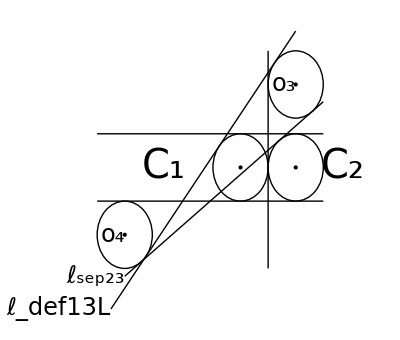

```mathematica
(*Originally from: Familyof5CirclesDisjointCorollary *)
(*taken from: SupportSkProperty3DisksCollinearNondisjont *)
(*δ=2/(√3);*)
δ=r;
 (*magnitude of x-coordinate of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;
ℓsep23Slope=(y3+2r)/(r+(2r)/y3(√(y3^2+4 r^2)+y3/2+2r));(*slope of line lsep for C2/C3*)
ℓsep23int=ℓsep23Slope*(-r)+y3/2;
γ=r(*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
Subscript[x, 4]=N[-(2r)/y3(√(y3^2+4 r^2)+y3/2+2r)](*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
y3=2.4648462125673194;
(*Subscript[s, 2]=(2r)/(Sqrt[t+δ+2r]Sqrt[t+δ-2r]);*) (*This is the slope of Subscript[m, 2](x), hence the mnemonic.*)
(*Subscript[s, 3]=(2r)/(Sqrt[t-δ+2r]Sqrt[t-δ-2r]);*) (*This is the slope of Subscript[m, 3](x), hence the mnemonic.*)
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];(*Three disks within horizontal slab between line Subscript[ℓ, 1] and line Subscript[ℓ, 2]*)
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{Subscript[x, 4]-r,r},{γ+r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{Subscript[x, 4]-r,-r},{γ+r,-r}}],Black,(*support line Subscript[ℓ, v], vertical*)Line[{{0,-2(r)-r},{0,y3+r}}](*,Black,(* support line Subscript[m, 3], vertical*)Line[{{δ+r,-(3r)},{δ+r,(3r)}}]*)}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r,0},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+(3r)/2,-3r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def13L]*)Line[{{Subscript[x, 4]-r/2,y3/(2r)*(Subscript[x, 4]-r/2)+(Sqrt[y3^2+4 r^2]+y3)/2},{γ,y3/(2r)*(γ)+(Sqrt[y3^2+4 r^2]+y3)/2}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep23]*)Line[{{Subscript[x, 4],ℓsep23Slope*(Subscript[x, 4])+ℓsep23int},{δ+r,ℓsep23Slope*(δ+r)+ℓsep23int}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, def13L],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]-r/2,y3/(2r)*(Subscript[x, 4]-r/2)+(Sqrt[y3^2+4 r^2]+y3)/2},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, sep23],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],ℓsep23Slope*(Subscript[x, 4])+ℓsep23int},{1,0}]];(*{Subscript[x, 4]-r-ε,k*(Subscript[x, 4]-r-ε)-k*δ/2+r}*)
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,y3}],Point[{Subscript[x, 4],-2r}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,y3},r],(*Disk C4 *)Circle[{Subscript[x, 4],-2r},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,y3},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],-2r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentiv *)(*see handwritten pages 11/20/19 for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21]
```

#### Finding an expression for y3

Evaluating with lemma vector distance, the line ℓ_sep23 and the center o_4 leads to

```mathematica
Clear[r,y3]
(*r=1;*)
k=(2*y3*(y3+2r))/(4r*y3+8*r^2+4r*√(y3^2+4 r^2));
```

```mathematica
(2r)/y3(√(y3^2+4 r^2)+y3/2+2r)*k+k*r-y3/2-2r=r*Sqrt[k^2+1]
```

Substituting in the alternative for slope k:

```mathematica
(2r)/y3(√(y3^2+4 r^2)+y3/2+2r)*(2*y3*(y3+2r))/(4r*y3+8*r^2+4r*√(y3^2+4 r^2))+(2*y3*(y3+2r))/(4r*y3+8*r^2+4r*√(y3^2+4 r^2))*r-y3/2-2r=r*Sqrt[((2*y3*(y3+2r))/(4r*y3+8*r^2+4r*√(y3^2+4 r^2)))^2+1]
```

We want to solve for y3

#### lhs

we will need to square the rhs, so let’s square the lhs

```mathematica
Clear[r,y3]
Expand[((2r)/y3(√(y3^2+4 r^2)+y3/2+2r)*(2*y3*(y3+2r))/(4r*y3+8*r^2+4r*√(y3^2+4 r^2))+(2*y3*(y3+2r))/(4r*y3+8*r^2+4r*√(y3^2+4 r^2))*r-y3/2-2r)^2]
```

4 r^2+2 r y3+y3^2/4+(512 r^6)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(768 r^5 y3)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(512 r^4 y3^2)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(192 r^3 y3^3)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(32 r^2 y3^4)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(256 r^5 √(4 r^2+y3^2))/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(384 r^4 y3 √(4 r^2+y3^2))/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(192 r^3 y3^2 √(4 r^2+y3^2))/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(32 r^2 y3^3 √(4 r^2+y3^2))/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)-(64 r^4)/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(80 r^3 y3)/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(32 r^2 y3^2)/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(4 r y3^3)/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(32 r^3 √(4 r^2+y3^2))/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(24 r^2 y3 √(4 r^2+y3^2))/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(4 r y3^2 √(4 r^2+y3^2))/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))

#### rhs

square the rhs

```mathematica
Expand[(r*Sqrt[((2*y3*(y3+2r))/(4r*y3+8*r^2+4r*√(y3^2+4 r^2)))^2+1])^2]
```

r^2+(16 r^4 y3^2)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(16 r^3 y3^3)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(4 r^2 y3^4)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)

Now, let’s eliminate denominators:

#### lhs

multiply lhs by highest denominator to eliminate

```mathematica
Simplify[((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)*(4 r^2+2 r y3+y3^2/4+(512 r^6)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(768 r^5 y3)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(512 r^4 y3^2)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(192 r^3 y3^3)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(32 r^2 y3^4)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(256 r^5 √(4 r^2+y3^2))/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(384 r^4 y3 √(4 r^2+y3^2))/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(192 r^3 y3^2 √(4 r^2+y3^2))/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(32 r^2 y3^3 √(4 r^2+y3^2))/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)-(64 r^4)/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(80 r^3 y3)/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(32 r^2 y3^2)/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(4 r y3^3)/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(32 r^3 √(4 r^2+y3^2))/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(24 r^2 y3 √(4 r^2+y3^2))/(8 r^2+4 r y3+4 r √(4 r^2+y3^2))-(4 r y3^2 √(4 r^2+y3^2))/(8 r^2+4 r y3+4 r √(4 r^2+y3^2)))]
```

8 r^2 y3^2 (4 r^2+2 r (y3+√(4 r^2+y3^2))+y3 (y3+√(4 r^2+y3^2)))

```mathematica
ExpandAll[8 r^2 y3^2 (4 r^2+2 r (y3+√(4 r^2+y3^2))+y3 (y3+√(4 r^2+y3^2)))]
```

32 r^4 y3^2+16 r^3 y3^3+8 r^2 y3^4+16 r^3 y3^2 √(4 r^2+y3^2)+8 r^2 y3^3 √(4 r^2+y3^2)

```mathematica
Collect[32 r^4 y3^2+16 r^3 y3^3+8 r^2 y3^4+16 r^3 y3^2 √(4 r^2+y3^2)+8 r^2 y3^3 √(4 r^2+y3^2),√(4 r^2+y3^2)]
```

32 r^4 y3^2+16 r^3 y3^3+8 r^2 y3^4+√(4 r^2+y3^2) (16 r^3 y3^2+8 r^2 y3^3)

#### rhs

Now do the same to the rhs

```mathematica
Simplify[(8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2*(r^2+(16 r^4 y3^2)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(16 r^3 y3^3)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2)+(4 r^2 y3^4)/((8 r^2+4 r y3+4 r √(4 r^2+y3^2))^2))]
```

4 r^2 (32 r^4+4 r y3^3+y3^4+16 r^3 (y3+√(4 r^2+y3^2))+4 r^2 y3 (3 y3+2 √(4 r^2+y3^2)))

```mathematica
ExpandAll[%]
```

128 r^6+64 r^5 y3+48 r^4 y3^2+16 r^3 y3^3+4 r^2 y3^4+64 r^5 √(4 r^2+y3^2)+32 r^4 y3 √(4 r^2+y3^2)

```mathematica
Collect[%, √(4 r^2+y3^2)]
```

128 r^6+64 r^5 y3+48 r^4 y3^2+16 r^3 y3^3+4 r^2 y3^4+(64 r^5+32 r^4 y3) √(4 r^2+y3^2)

#### lhs, collect radicals

```mathematica
Collect[Expand[(*lhs radicals*)√(4 r^2+y3^2) (16 r^3 y3^2+8 r^2 y3^3)-(*rhs radicals*)(64 r^5+32 r^4 y3) √(4 r^2+y3^2)],√(4 r^2+y3^2)]
```

```mathematica
√(4 r^2+y3^2) (-64 r^5-32 r^4 y3+16 r^3 y3^2+8 r^2 y3^3)
```

#### rhs, collect other terms

```mathematica
Expand[(*lhs terms*)(128 r^6+64 r^5 y3+48 r^4 y3^2+16 r^3 y3^3+4 r^2 y3^4)-(*rhs terms*)(32 r^4 y3^2+16 r^3 y3^3+8 r^2 y3^4)]
```

128 r^6+64 r^5 y3+16 r^4 y3^2-4 r^2 y3^4

#### lhs

square lhs to eliminate radical

```mathematica
Expand[(√(4 r^2+y3^2) (-64 r^5-32 r^4 y3+16 r^3 y3^2+8 r^2 y3^3))^2]
```

16384 r^12+16384 r^11 y3-4096 r^9 y3^3-2048 r^8 y3^4-1024 r^7 y3^5+256 r^5 y3^7+64 r^4 y3^8

#### rhs

also square the rhs

```mathematica
Expand[(128 r^6+64 r^5 y3+16 r^4 y3^2-4 r^2 y3^4)^2]
```

16384 r^12+16384 r^11 y3+8192 r^10 y3^2+2048 r^9 y3^3-768 r^8 y3^4-512 r^7 y3^5-128 r^6 y3^6+16 r^4 y3^8

#### combine lhs and rhs (lhs-rhs)

```mathematica
Expand[(*lhs*)(16384 r^12+16384 r^11 y3-4096 r^9 y3^3-2048 r^8 y3^4-1024 r^7 y3^5+256 r^5 y3^7+64 r^4 y3^8)-(*rhs*)(16384 r^12+16384 r^11 y3+8192 r^10 y3^2+2048 r^9 y3^3-768 r^8 y3^4-512 r^7 y3^5-128 r^6 y3^6+16 r^4 y3^8)]
```

-8192 r^10 y3^2-6144 r^9 y3^3-1280 r^8 y3^4-512 r^7 y3^5+128 r^6 y3^6+256 r^5 y3^7+48 r^4 y3^8

#### Solve for y3

```mathematica
NSolve[-8192 y3^2-6144 y3^3-1280 y3^4-512 y3^5+128 y3^6+256 y3^7+48 y3^8==0,y3]
```

{{y3→-4.15287},{y3→-2.},{y3→-2.},{y3→0.},{y3→0.},{y3→0.177343+2.03391 ⅈ},{y3→0.177343-2.03391 ⅈ},{y3→2.46485}}

```mathematica
(*r=1*)
Clear[r]
Solve[-8192 r^10 y3^2-6144 r^9 y3^3-1280 r^8 y3^4-512 r^7 y3^5+128 r^6 y3^6+256 r^5 y3^7+48 r^4 y3^8==0,y3](*Can we rewrite general solution to be manageable*)
```

{{y3→0},{y3→0},{y3→-2 r},{y3→-2 r},{y3→-r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))-1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→-r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→-r/3-1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))-1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→-r/3-1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))}}

Simplified form for our polynomial:

```mathematica
Cancel[(-8192 r^10 y3^2-6144 r^9 y3^3-1280 r^8 y3^4-512 r^7 y3^5+128 r^6 y3^6+256 r^5 y3^7+48 r^4 y3^8)/(r^4*y3^2)]
```

-16 (512 r^6+384 r^5 y3+80 r^4 y3^2+32 r^3 y3^3-8 r^2 y3^4-16 r y3^5-3 y3^6)

```mathematica
Clear[r,y3]
-(512 r^6+384 r^5 y3+80 r^4 y3^2+32 r^3 y3^3-8 r^2 y3^4-16 r y3^5-3 y3^6)
```

-512 r^6-384 r^5 y3-80 r^4 y3^2-32 r^3 y3^3+8 r^2 y3^4+16 r y3^5+3 y3^6

```mathematica
Clear[r,y3]
r=1
NSolve[512 r^6+384 r^5 y3+80 r^4 y3^2+32 r^3 y3^3-8 r^2 y3^4-16 r y3^5-3 y3^6==0,y3]
```

1

{{y3→-4.15287},{y3→-2.},{y3→-2.},{y3→0.177343-2.03391 ⅈ},{y3→0.177343+2.03391 ⅈ},{y3→2.46485}}

The following is the general solution for y3:

```mathematica
r=1
N[-r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))]
```

1

2.46485+0. ⅈ

```mathematica
Clear[r]
Simplify[-r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))]
```

-r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))

## Tangent Critical F4, case (v)(revised 10/27/10),γ=r, ℓ_def13L supports C4 on RHS, ℓ_sep23 supports C4 on left (above)

1

-5.68585

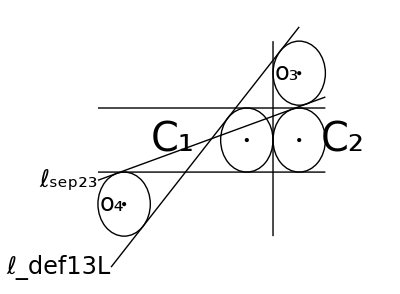

```mathematica
(*Originally from: Familyof5CirclesDisjointCorollary *)
(*taken from: SupportSkProperty3DisksCollinearNondisjont *)
(*δ=2/(√3);*)
δ=r;
 (*magnitude of x-coordinate of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;
ℓsep23Slope=y3/(2 r+y3+√(4 r^2+y3^2));(*slope of line lsep for C2/C3*)
ℓsep23int=ℓsep23Slope*(-r)+y3/2;
γ=r(*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
Subscript[x, 4]=-(2r)/y3(√(y3^2+4 r^2)+y3/2+2r)(*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
y3=2.0875673686822096;
(*Subscript[s, 2]=(2r)/(Sqrt[t+δ+2r]Sqrt[t+δ-2r]);*) (*This is the slope of Subscript[m, 2](x), hence the mnemonic.*)
(*Subscript[s, 3]=(2r)/(Sqrt[t-δ+2r]Sqrt[t-δ-2r]);*) (*This is the slope of Subscript[m, 3](x), hence the mnemonic.*)
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];(*Three disks within horizontal slab between line Subscript[ℓ, 1] and line Subscript[ℓ, 2]*)
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{Subscript[x, 4]-r,r},{γ+r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{Subscript[x, 4]-r,-r},{γ+r,-r}}],Black,(*support line Subscript[ℓ, v], vertical*)Line[{{0,-2(r)-r},{0,y3+r}}](*,Black,(* support line Subscript[m, 3], vertical*)Line[{{δ+r,-(3r)},{δ+r,(3r)}}]*)}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r,0},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+(3r)/2,-3r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def13L]*)Line[{{Subscript[x, 4]-r/2,y3/(2r)*(Subscript[x, 4]-r/2)+(Sqrt[y3^2+4 r^2]+y3)/2},{γ,y3/(2r)*(γ)+(Sqrt[y3^2+4 r^2]+y3)/2}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep23]*)Line[{{Subscript[x, 4]-r,ℓsep23Slope*(Subscript[x, 4]-r)+ℓsep23int},{δ+r,ℓsep23Slope*(δ+r)+ℓsep23int}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, def13L],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]-r/2,y3/(2r)*(Subscript[x, 4]-r/2)+(Sqrt[y3^2+4 r^2]+y3)/2},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, sep23],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]-r,ℓsep23Slope*(Subscript[x, 4]-r)+ℓsep23int},{1,0}]];(*{Subscript[x, 4]-r-ε,k*(Subscript[x, 4]-r-ε)-k*δ/2+r}*)
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,y3}],Point[{Subscript[x, 4],-2r}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,y3},r],(*Disk C4 *)Circle[{Subscript[x, 4],-2r},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,y3},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],-2r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentvi *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21]
```

slope for ellsep23

```mathematica
Clear[r,y3]
Simplify[2/(1+2/y3(√(y3^2+4 r^2)+y3/2+2r))]
```

y3/(2 r+y3+√(4 r^2+y3^2))

### Alternative description for y3

```mathematica
Expand[((2r+ε)/(2 r+2r+ε+√(4 r^2+(2r+ε)^2)))^2==((√((2r+ε)^2-4 r^2))/(2r))^2]
```

(4 r^2)/((4 r+ε+√(4 r^2+(2 r+ε)^2))^2)+(4 r ε)/((4 r+ε+√(4 r^2+(2 r+ε)^2))^2)+ε^2/((4 r+ε+√(4 r^2+(2 r+ε)^2))^2)==ε/r+ε^2/(4 r^2)

```mathematica
Simplify[MultiplySides[(4 r^2)/((4 r+ε+√(4 r^2+(2 r+ε)^2))^2)+(4 r ε)/((4 r+ε+√(4 r^2+(2 r+ε)^2))^2)+ε^2/((4 r+ε+√(4 r^2+(2 r+ε)^2))^2)==ε/r+ε^2/(4 r^2),4 r^2*(4 r+ε+√(4 r^2+(2 r+ε)^2))^2]]
```

Piecewise[{{4 r^2 (2 r+ε)^2==ε (4 r+ε) (4 r+ε+√(8 r^2+4 r ε+ε^2))^2, r (4 r+ε+√(8 r^2+4 r ε+ε^2))≠0}, {(2 r+ε)^2/((4 r+ε+√(8 r^2+4 r ε+ε^2))^2)==(ε (4 r+ε))/(4 r^2), True}}]

```mathematica
ExpandAll[4 r^2 (2 r+ε)^2==ε (4 r+ε) (4 r+ε+√(8 r^2+4 r ε+ε^2))^2]
```

16 r^4+16 r^3 ε+4 r^2 ε^2==96 r^3 ε+72 r^2 ε^2+20 r ε^3+2 ε^4+32 r^2 ε √(8 r^2+4 r ε+ε^2)+16 r ε^2 √(8 r^2+4 r ε+ε^2)+2 ε^3 √(8 r^2+4 r ε+ε^2)

```mathematica
Collect[16 r^4+16 r^3 ε+4 r^2 ε^2==96 r^3 ε+72 r^2 ε^2+20 r ε^3+2 ε^4+32 r^2 ε √(8 r^2+4 r ε+ε^2)+16 r ε^2 √(8 r^2+4 r ε+ε^2)+2 ε^3 √(8 r^2+4 r ε+ε^2),√(8 r^2+4 r ε+ε^2)]
```

16 r^4+16 r^3 ε+4 r^2 ε^2==96 r^3 ε+72 r^2 ε^2+20 r ε^3+2 ε^4+√(8 r^2+4 r ε+ε^2) (32 r^2 ε+16 r ε^2+2 ε^3)

```mathematica
AddSides[16 r^4+16 r^3 ε+4 r^2 ε^2==96 r^3 ε+72 r^2 ε^2+20 r ε^3+2 ε^4+√(8 r^2+4 r ε+ε^2) (32 r^2 ε+16 r ε^2+2 ε^3),-(96 r^3 ε+72 r^2 ε^2+20 r ε^3+2 ε^4)]
```

16 r^4-80 r^3 ε-68 r^2 ε^2-20 r ε^3-2 ε^4==√(8 r^2+4 r ε+ε^2) (32 r^2 ε+16 r ε^2+2 ε^3)

```mathematica
Expand[(16 r^4-80 r^3 ε-68 r^2 ε^2-20 r ε^3-2 ε^4)^2==(√(8 r^2+4 r ε+ε^2) (32 r^2 ε+16 r ε^2+2 ε^3))^2]
```

256 r^8-2560 r^7 ε+4224 r^6 ε^2+10240 r^5 ε^3+7760 r^4 ε^4+3040 r^3 ε^5+672 r^2 ε^6+80 r ε^7+4 ε^8==8192 r^6 ε^2+12288 r^5 ε^3+8192 r^4 ε^4+3072 r^3 ε^5+672 r^2 ε^6+80 r ε^7+4 ε^8

```mathematica
AddSides[256 r^8-2560 r^7 ε+4224 r^6 ε^2+10240 r^5 ε^3+7760 r^4 ε^4+3040 r^3 ε^5+672 r^2 ε^6+80 r ε^7+4 ε^8==8192 r^6 ε^2+12288 r^5 ε^3+8192 r^4 ε^4+3072 r^3 ε^5+672 r^2 ε^6+80 r ε^7+4 ε^8,-(8192 r^6 ε^2+12288 r^5 ε^3+8192 r^4 ε^4+3072 r^3 ε^5+672 r^2 ε^6+80 r ε^7+4 ε^8)]
```

256 r^8-2560 r^7 ε-3968 r^6 ε^2-2048 r^5 ε^3-432 r^4 ε^4-32 r^3 ε^5==0

```mathematica
NSolve[256 r^8-2560 r^7 ε-3968 r^6 ε^2-2048 r^5 ε^3-432 r^4 ε^4-32 r^3 ε^5==0,ε]
```

{{ε→-2. r},{ε→-2. r},{ε→(-5.16902+1.4803×10^-16 ⅈ) r},{ε→(0.0875674+1.11022×10^-16 ⅈ) r},{ε→(-4.41855-2.22045×10^-16 ⅈ) r}}

### Derive value for y3 based on two values of k

The slope for ellsep23 from parallel to o3, o4

```mathematica
k=y3/(2 r+y3+√(4 r^2+y3^2))
```

the slope for the line from distance vector lemma

```mathematica
k=(√(y3^2-4 r^2))/(2r)
```

Set k=k and square both sides, eliminate radical rhs

```mathematica
Clear[r,y3]
Expand[(y3/(2 r+y3+√(4 r^2+y3^2)))^2==((√(y3^2-4 r^2))/(2r))^2]
```

y3^2/((2 r+y3+√(4 r^2+y3^2))^2)==-1+y3^2/(4 r^2)

multiply clear fractions

```mathematica
MultiplySides[y3^2/((2 r+y3+√(4 r^2+y3^2))^2)==-1+y3^2/(4 r^2),4 r^2(2 r+y3+√(4 r^2+y3^2))^2]
```

Piecewise[{{4 r^2 y3^2==4 r^2 (-1+y3^2/(4 r^2)) (2 r+y3+√(4 r^2+y3^2))^2, 4 r^2 (2 r+y3+√(4 r^2+y3^2))^2≠0}, {y3^2/((2 r+y3+√(4 r^2+y3^2))^2)==-1+y3^2/(4 r^2), True}}]

```mathematica
ExpandAll[4 r^2 y3^2==4 r^2 (-1+y3^2/(4 r^2)) (2 r+y3+√(4 r^2+y3^2))^2]
```

4 r^2 y3^2==-32 r^4-16 r^3 y3+4 r y3^3+2 y3^4-16 r^3 √(4 r^2+y3^2)-8 r^2 y3 √(4 r^2+y3^2)+4 r y3^2 √(4 r^2+y3^2)+2 y3^3 √(4 r^2+y3^2)

```mathematica
Collect[4 r^2 y3^2==-32 r^4-16 r^3 y3+4 r y3^3+2 y3^4-16 r^3 √(4 r^2+y3^2)-8 r^2 y3 √(4 r^2+y3^2)+4 r y3^2 √(4 r^2+y3^2)+2 y3^3 √(4 r^2+y3^2),√(4 r^2+y3^2)]
```

4 r^2 y3^2==-32 r^4-16 r^3 y3+4 r y3^3+2 y3^4+√(4 r^2+y3^2) (-16 r^3-8 r^2 y3+4 r y3^2+2 y3^3)

Isolate the radicals on one side

```mathematica
AddSides[4 r^2 y3^2==-32 r^4-16 r^3 y3+4 r y3^3+2 y3^4+√(4 r^2+y3^2) (-16 r^3-8 r^2 y3+4 r y3^2+2 y3^3),-(-32 r^4-16 r^3 y3+4 r y3^3+2 y3^4)]
```

32 r^4+16 r^3 y3+4 r^2 y3^2-4 r y3^3-2 y3^4==√(4 r^2+y3^2) (-16 r^3-8 r^2 y3+4 r y3^2+2 y3^3)

square to eliminate radical

```mathematica
Expand[(32 r^4+16 r^3 y3+4 r^2 y3^2-4 r y3^3-2 y3^4)^2==(√(4 r^2+y3^2) (-16 r^3-8 r^2 y3+4 r y3^2+2 y3^3))^2]
```

1024 r^8+1024 r^7 y3+512 r^6 y3^2-128 r^5 y3^3-240 r^4 y3^4-96 r^3 y3^5+16 r y3^7+4 y3^8==1024 r^8+1024 r^7 y3-256 r^5 y3^3-128 r^4 y3^4-64 r^3 y3^5+16 r y3^7+4 y3^8

combine on lhs

```mathematica
AddSides[1024 r^8+1024 r^7 y3+512 r^6 y3^2-128 r^5 y3^3-240 r^4 y3^4-96 r^3 y3^5+16 r y3^7+4 y3^8==1024 r^8+1024 r^7 y3-256 r^5 y3^3-128 r^4 y3^4-64 r^3 y3^5+16 r y3^7+4 y3^8,-(1024 r^8+1024 r^7 y3-256 r^5 y3^3-128 r^4 y3^4-64 r^3 y3^5+16 r y3^7+4 y3^8)]
```

512 r^6 y3^2+128 r^5 y3^3-112 r^4 y3^4-32 r^3 y3^5==0

```mathematica
Clear[r,y3]
Collect[512 r^6 y3^2+128 r^5 y3^3-112 r^4 y3^4-32 r^3 y3^5,y3]
```

512 r^6 y3^2+128 r^5 y3^3-112 r^4 y3^4-32 r^3 y3^5

```mathematica
Clear[r,y3]
r=1
NSolve[512 r^6 y3^2+128 r^5 y3^3-112 r^4 y3^4-32 r^3 y3^5==0,y3]
```

1

Simplify the polynomial

```mathematica
Cancel[(512 r^6 y3^2+128 r^5 y3^3-112 r^4 y3^4-32 r^3 y3^5)/(r^3*y3^2)]
```

16 (32 r^3+8 r^2 y3-7 r y3^2-2 y3^3)

```mathematica
-(32 r^3+8 r^2 y3-7 r y3^2-2 y3^3)
```

-32 r^3-8 r^2 y3+7 r y3^2+2 y3^3

```mathematica
Clear[r,y3]
(*r=1*)
Solve[512 r^6 y3^2+128 r^5 y3^3-112 r^4 y3^4-32 r^3 y3^5==0,y3,PositiveReals]
```

{{y3→ConditionalExpression[Root[-32 r^3-8 r^2 #1+7 r #1^2+2 #1^3&,3], r>0]}}

```mathematica
Solve[-32 r^3-8 r^2 y3+7 r y3^2+2 y3^3==0,y3]
```

{{y3→1/6 (-7 r+(97 r)/(881+24 ⅈ √237)^(1/3)+(881+24 ⅈ √237)^(1/3) r)},{y3→-(7 r)/6-(97 (1+ⅈ √3) r)/(12 (881+24 ⅈ √237)^(1/3))-1/12 (1-ⅈ √3) (881+24 ⅈ √237)^(1/3) r},{y3→-(7 r)/6-(97 (1-ⅈ √3) r)/(12 (881+24 ⅈ √237)^(1/3))-1/12 (1+ⅈ √3) (881+24 ⅈ √237)^(1/3) r}}

## Tangent Critical F4, case (vi)(revised 10/27/20),γ=r, ℓ_def13L supports C4 on RHS, ℓ_sep supports C4 on right (from below), ℓ_1 supports C4

1

-1.94137

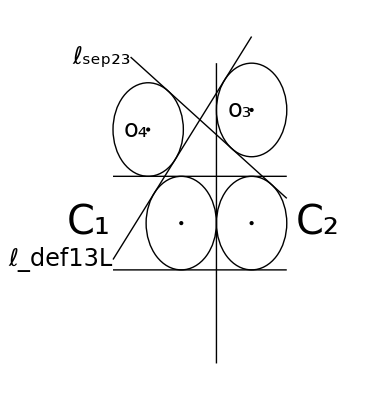

```mathematica
(*Originally from: Familyof5CirclesDisjointCorollary *)
(*taken from: SupportSkProperty3DisksCollinearNondisjont *)
(*δ=2/(√3);*)
δ=r;
 (*magnitude of x-coordinate of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;
ℓsep23Slope=-y3/(-2 r+y3+√(4 r^2+y3^2))(*(-2*y3*(y3+2r))/(4r*y3+8 r^2+4r √(y3^2+4 r^2))*);(*(-(y3+2r))/(r+(2r)/y3(√(y3^2+4 r^2)+y3/2+2r))*)(*slope of line lsep for C2/C3*)
ℓsep23int=ℓsep23Slope*(-r)+y3/2;
γ=r(*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
Subscript[x, 4]=N[-(2r)/y3(√(y3^2+4 r^2)+y3/2-2r)](*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
y3=2.4185451392580335(*3.169022229424176 not correct, but is real>0*);
(*Subscript[s, 2]=(2r)/(Sqrt[t+δ+2r]Sqrt[t+δ-2r]);*) (*This is the slope of Subscript[m, 2](x), hence the mnemonic.*)
(*Subscript[s, 3]=(2r)/(Sqrt[t-δ+2r]Sqrt[t-δ-2r]);*) (*This is the slope of Subscript[m, 3](x), hence the mnemonic.*)
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];(*Three disks within horizontal slab between line Subscript[ℓ, 1] and line Subscript[ℓ, 2]*)
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{Subscript[x, 4]-r,r},{γ+r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{Subscript[x, 4]-r,-r},{γ+r,-r}}],Black,(*support line Subscript[ℓ, v], vertical*)Line[{{0,-2(r)-r},{0,y3+r}}](*,Black,(* support line Subscript[m, 3], vertical*)Line[{{δ+r,-(3r)},{δ+r,(3r)}}]*)}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r,0},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+(3r)/2,-3r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def13L]*)Line[{{Subscript[x, 4]-r,y3/(2r)*(Subscript[x, 4]-r)+(Sqrt[y3^2+4 r^2]+y3)/2},{γ,y3/(2r)*(γ)+(Sqrt[y3^2+4 r^2]+y3)/2}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep23]*)Line[{{Subscript[x, 4]-r/2,ℓsep23Slope*(Subscript[x, 4]-r/2)+ℓsep23int},{δ+r,ℓsep23Slope*(δ+r)+ℓsep23int}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, def13L],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]-r,y3/(2r)*(Subscript[x, 4]-r)+(Sqrt[y3^2+4 r^2]+y3)/2},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, sep23],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]-r/2,ℓsep23Slope*(Subscript[x, 4]-r/2)+ℓsep23int},{1,0}]];(*{Subscript[x, 4]-r-ε,k*(Subscript[x, 4]-r-ε)-k*δ/2+r}*)
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,y3}],Point[{Subscript[x, 4],2r}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,y3},r],(*Disk C4 *)Circle[{Subscript[x, 4],2r},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,y3},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],2r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentv *)(*see handwritten pages 11/20/19 for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21]
```

#### Solving for y3 given two values for the slope of ℓ_sep23

We have an equation for k

```mathematica
(-2r)/y3(√(y3^2+4 r^2)+y3/2-2r)*k-k*r+y3/2-2r=r*Sqrt[k^2+1]
```

We have another value for k derived as a definite support

```mathematica
k=-y3/(-2 r+y3+√(4 r^2+y3^2))
```

Substitute in the value for k into the equation

```mathematica
Clear[r,y3,k]
{(-2r)/y3(√(y3^2+4 r^2)+y3/2-2r)*k-k*r+y3/2-2r==r*Sqrt[k^2+1]}/.k->-y3/(-2 r+y3+√(4 r^2+y3^2))
```

{-2 r+y3/2+(r y3)/(-2 r+y3+√(4 r^2+y3^2))+(2 r (-2 r+y3/2+√(4 r^2+y3^2)))/(-2 r+y3+√(4 r^2+y3^2))==r √(1+y3^2/((-2 r+y3+√(4 r^2+y3^2))^2))}

Square both sides to eliminate radical on rhs

```mathematica
Expand[(-2 r+y3/2+(r y3)/(-2 r+y3+√(4 r^2+y3^2))+(2 r (-2 r+y3/2+√(4 r^2+y3^2)))/(-2 r+y3+√(4 r^2+y3^2)))^2==(r √(1+y3^2/((-2 r+y3+√(4 r^2+y3^2))^2)))^2]
```

4 r^2-2 r y3+y3^2/4+(32 r^4)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 y3)/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(16 r^3)/(-2 r+y3+√(4 r^2+y3^2))-(12 r^2 y3)/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3^2)/(-2 r+y3+√(4 r^2+y3^2))-(8 r^2 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2))==r^2+(r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2)

```mathematica
MultiplySides[4 r^2-2 r y3+y3^2/4+(32 r^4)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 y3)/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(16 r^3)/(-2 r+y3+√(4 r^2+y3^2))-(12 r^2 y3)/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3^2)/(-2 r+y3+√(4 r^2+y3^2))-(8 r^2 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2))==r^2+(r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2),(-2 r+y3+√(4 r^2+y3^2))^2]
```

Piecewise[{{(-2 r+y3+√(4 r^2+y3^2))^2 (4 r^2-2 r y3+y3^2/4+(32 r^4)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 y3)/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(16 r^3)/(-2 r+y3+√(4 r^2+y3^2))-(12 r^2 y3)/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3^2)/(-2 r+y3+√(4 r^2+y3^2))-(8 r^2 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2)))==(-2 r+y3+√(4 r^2+y3^2))^2 (r^2+(r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2)), (-2 r+y3+√(4 r^2+y3^2))^2≠0}, {4 r^2-2 r y3+y3^2/4+(32 r^4)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 y3)/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(16 r^3)/(-2 r+y3+√(4 r^2+y3^2))-(12 r^2 y3)/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3^2)/(-2 r+y3+√(4 r^2+y3^2))-(8 r^2 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2))==r^2+(r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2), True}}]

```mathematica
Cancel[(-2 r+y3+√(4 r^2+y3^2))^2 (4 r^2-2 r y3+y3^2/4+(32 r^4)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 y3)/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2)-(16 r^3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(8 r^2 y3 √(4 r^2+y3^2))/((-2 r+y3+√(4 r^2+y3^2))^2)+(16 r^3)/(-2 r+y3+√(4 r^2+y3^2))-(12 r^2 y3)/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3^2)/(-2 r+y3+√(4 r^2+y3^2))-(8 r^2 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2))+(2 r y3 √(4 r^2+y3^2))/(-2 r+y3+√(4 r^2+y3^2)))==(-2 r+y3+√(4 r^2+y3^2))^2 (r^2+(r^2 y3^2)/((-2 r+y3+√(4 r^2+y3^2))^2))]
```

1/2 (4 r^2 y3^2-2 r y3^3+y3^4-2 r y3^2 √(4 r^2+y3^2)+y3^3 √(4 r^2+y3^2))==-r^2 (-8 r^2+4 r y3-3 y3^2+4 r √(4 r^2+y3^2)-2 y3 √(4 r^2+y3^2))

```mathematica
Collect[1/2 (4 r^2 y3^2-2 r y3^3+y3^4-2 r y3^2 √(4 r^2+y3^2)+y3^3 √(4 r^2+y3^2))==-r^2 (-8 r^2+4 r y3-3 y3^2+4 r √(4 r^2+y3^2)-2 y3 √(4 r^2+y3^2)),√(4 r^2+y3^2)]
```

1/2 √(4 r^2+y3^2) (-2 r y3^2+y3^3)+1/2 (4 r^2 y3^2-2 r y3^3+y3^4)==-r^2 (-8 r^2+4 r y3-3 y3^2)-r^2 (4 r-2 y3) √(4 r^2+y3^2)

```mathematica
AddSides[1/2 √(4 r^2+y3^2) (-2 r y3^2+y3^3)+1/2 (4 r^2 y3^2-2 r y3^3+y3^4)==-r^2 (-8 r^2+4 r y3-3 y3^2)-r^2 (4 r-2 y3) √(4 r^2+y3^2),-1/2 √(4 r^2+y3^2) (-2 r y3^2+y3^3)+r^2 (-8 r^2+4 r y3-3 y3^2)]
```

r^2 (-8 r^2+4 r y3-3 y3^2)+1/2 (4 r^2 y3^2-2 r y3^3+y3^4)==-r^2 (4 r-2 y3) √(4 r^2+y3^2)-1/2 √(4 r^2+y3^2) (-2 r y3^2+y3^3)

```mathematica
Collect[r^2 (-8 r^2+4 r y3-3 y3^2)+1/2 (4 r^2 y3^2-2 r y3^3+y3^4)==-r^2 (4 r-2 y3) √(4 r^2+y3^2)-1/2 √(4 r^2+y3^2) (-2 r y3^2+y3^3),√(4 r^2+y3^2)]
```

r^2 (-8 r^2+4 r y3-3 y3^2)+1/2 (4 r^2 y3^2-2 r y3^3+y3^4)==√(4 r^2+y3^2) (-4 r^3+2 r^2 y3+r y3^2-y3^3/2)

Square both sides to eliminate radical

```mathematica
Expand[(r^2 (-8 r^2+4 r y3-3 y3^2)+1/2 (4 r^2 y3^2-2 r y3^3+y3^4))^2==(√(4 r^2+y3^2) (-4 r^3+2 r^2 y3+r y3^2-y3^3/2))^2]
```

64 r^8-64 r^7 y3+32 r^6 y3^2+8 r^5 y3^3-15 r^4 y3^4+6 r^3 y3^5-r y3^7+y3^8/4==64 r^8-64 r^7 y3+16 r^5 y3^3-8 r^4 y3^4+4 r^3 y3^5-r y3^7+y3^8/4

Collect everything to one side

```mathematica
AddSides[64 r^8-64 r^7 y3+32 r^6 y3^2+8 r^5 y3^3-15 r^4 y3^4+6 r^3 y3^5-r y3^7+y3^8/4==64 r^8-64 r^7 y3+16 r^5 y3^3-8 r^4 y3^4+4 r^3 y3^5-r y3^7+y3^8/4,-(64 r^8-64 r^7 y3+16 r^5 y3^3-8 r^4 y3^4+4 r^3 y3^5-r y3^7+y3^8/4)]
```

32 r^6 y3^2-8 r^5 y3^3-7 r^4 y3^4+2 r^3 y3^5==0

```mathematica
NSolve[32 r^6 y3^2-8 r^5 y3^3-7 r^4 y3^4+2 r^3 y3^5==0,y3]
```

{{y3→0},{y3→0},{y3→(3.16902-1.4803×10^-16 ⅈ) r},{y3→(-2.08757-1.11022×10^-16 ⅈ) r},{y3→(2.41855+2.22045×10^-16 ⅈ) r}}

```mathematica
Clear[r,y3]
r=1;
NSolve[32 r^6 y3^2-8 r^5 y3^3-7 r^4 y3^4+2 r^3 y3^5==0&&r>0,y3]
N[(7 r)/6+(97 (-1)^(5/6) (1-ⅈ √3) r)/(12 (881 ⅈ+24 √237)^(1/3))-1/12 (-1)^(1/6) (1+ⅈ √3) (881 ⅈ+24 √237)^(1/3) r]
```

{{y3→-2.08757},{y3→0.},{y3→0.},{y3→2.41855},{y3→3.16902}}

```mathematica
2.4185451392580335+2.220446049250313*^-16 ⅈ
Factor[881]
881^2+24^2*237
881
912673
PrimeQ[881]
True
june
tegan
N[(-1)^(1/6)]
0.8660254037844387+0.49999999999999994 ⅈ
N[(-1)^(5/6)]
-0.8660254037844387+0.49999999999999994 ⅈ
```

Plot the graph to verify real roots

```mathematica
Clear[r,y3,x]
32 r^6 y3^2-8 r^5 y3^3-7 r^4 y3^4+2 r^3 y3^5/.y3->x
```

```mathematica
32 r^6 x^2-8 r^5 x^3-7 r^4 x^4+2 r^3 x^5/.r->1
```

32 x^2-8 x^3-7 x^4+2 x^5

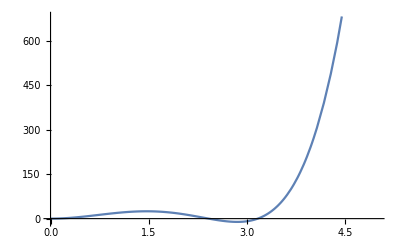

```mathematica
Plot[32 x^2-8 x^3-7 x^4+2 x^5,{x,0,5}]
```

Intermediate value theorem with r=1

```mathematica
32 x^2-8 x^3-7 x^4+2 x^5/.x->2
```

16

```mathematica
32 x^2-8 x^3-7 x^4+2 x^5/.x->3
```

-9

With the positive and negative values of p(x) at x=2 and x=3, we see that the polynomial has a real root in the interval [2,3]

#### Attempt to rewrite expression (solution) symbolically, not numerically

```mathematica
Clear[r,y3]
Solve[32 r^6 y3^2-8 r^5 y3^3-7 r^4 y3^4+2 r^3 y3^5==0,y3,PositiveReals]
```

{{y3→ConditionalExpression[Root[32 r^3-8 r^2 #1-7 r #1^2+2 #1^3&,2], r>0]},{y3→ConditionalExpression[Root[32 r^3-8 r^2 #1-7 r #1^2+2 #1^3&,3], r>0]}}

```mathematica
Clear[r,y3]
Solve[32 r^6 y3^2-8 r^5 y3^3-7 r^4 y3^4+2 r^3 y3^5==0,y3]
```

{{y3→0},{y3→0},{y3→1/6 (7 r-(97 (-1)^(5/6) r)/(881 ⅈ+24 √237)^(1/3)+(-1)^(1/6) (881 ⅈ+24 √237)^(1/3) r)},{y3→(7 r)/6+(97 (-1)^(5/6) (1+ⅈ √3) r)/(12 (881 ⅈ+24 √237)^(1/3))-1/12 (-1)^(1/6) (1-ⅈ √3) (881 ⅈ+24 √237)^(1/3) r},{y3→(7 r)/6+(97 (-1)^(5/6) (1-ⅈ √3) r)/(12 (881 ⅈ+24 √237)^(1/3))-1/12 (-1)^(1/6) (1+ⅈ √3) (881 ⅈ+24 √237)^(1/3) r}}

```mathematica
Clear[r]
Simplify[(7 r)/6+(97 (-1)^(5/6) (1-ⅈ √3) r)/(12 (881 ⅈ+24 √237)^(1/3))-1/12 (-1)^(1/6) (1+ⅈ √3) (881 ⅈ+24 √237)^(1/3) r]
```

1/6 (7+(97 ⅈ)/(881 ⅈ+24 √237)^(1/3)-ⅈ (881 ⅈ+24 √237)^(1/3)) r

```mathematica
Together[1/6 (7+(97 ⅈ)/(881 ⅈ+24 √237)^(1/3)-ⅈ (881 ⅈ+24 √237)^(1/3)) r](*How do we rewrite this as a real expression?, especially since r>0*)
```

((97 ⅈ+7 (881 ⅈ+24 √237)^(1/3)-ⅈ (881 ⅈ+24 √237)^(2/3)) r)/(6 (881 ⅈ+24 √237)^(1/3))

```mathematica
(*Clear[r,y3]*)
r=1
NSolve[32 r^6 y3^2-8 r^5 y3^3-7 r^4 y3^4+2 r^3 y3^5==0,y3,PositiveReals]
```

1

{{y3→2.41855},{y3→3.16902}}

```mathematica
r=1
N[Root[32 r^3-8 r^2 #1-7 r #1^2+2 #1^3&,2]]
```

1

2.41855

```mathematica
Clear[r]
(*r=1*)
Solve[32 r^3-8 r^2 x-7 r x^2+2 x^3==0,x]
```

{{x→1/6 (7 r-(97 (-1)^(5/6) r)/(881 ⅈ+24 √237)^(1/3)+(-1)^(1/6) (881 ⅈ+24 √237)^(1/3) r)},{x→(7 r)/6+(97 (-1)^(5/6) (1+ⅈ √3) r)/(12 (881 ⅈ+24 √237)^(1/3))-1/12 (-1)^(1/6) (1-ⅈ √3) (881 ⅈ+24 √237)^(1/3) r},{x→(7 r)/6+(97 (-1)^(5/6) (1-ⅈ √3) r)/(12 (881 ⅈ+24 √237)^(1/3))-1/12 (-1)^(1/6) (1+ⅈ √3) (881 ⅈ+24 √237)^(1/3) r}}

```mathematica
r=1
N[1/6 (7 r-(97 (-1)^(5/6) r)/(881 ⅈ+24 √237)^(1/3)+(-1)^(1/6) (881 ⅈ+24 √237)^(1/3) r)]
```

1

3.16902-1.4803×10^-16 ⅈ

```mathematica
N[(7 r)/6+(97 (-1)^(5/6) (1+ⅈ √3) r)/(12 (881 ⅈ+24 √237)^(1/3))-1/12 (-1)^(1/6) (1-ⅈ √3) (881 ⅈ+24 √237)^(1/3) r]
```

-2.08757-1.11022×10^-16 ⅈ

```mathematica
N[97/Surd[912673,6]-Surd[912673,6]]
```

0.

```mathematica
1.173694012766495+Pi
```

4.31529

```mathematica
N[(3*Pi)/2]
```

4.71239

```mathematica
N[(7 r)/6+(97 (-1)^(5/6) (1-ⅈ √3) r)/(12 (881 ⅈ+24 √237)^(1/3))-1/12 (-1)^(1/6) (1+ⅈ √3) (881 ⅈ+24 √237)^(1/3) r]
```

2.41855+2.22045×10^-16 ⅈ

```mathematica
Clear[r]
r=1
N[r/6*(7-97/Surd[912673,6]-Surd[912673,6])]
```

1

-2.11629

```mathematica
Clear[r]
r=1;
ϕ=ArcTan[881/(24*Sqrt[237])];
N[r/6*(7+Sin[ϕ/3]*(97/Surd[912673,6]+Surd[912673,6]))]
```

2.41855

## Tangent Critical F4, case (vii) , ℓ_def13R supports C4 on LHS, ℓ_sep23RL supports C4 on left

2

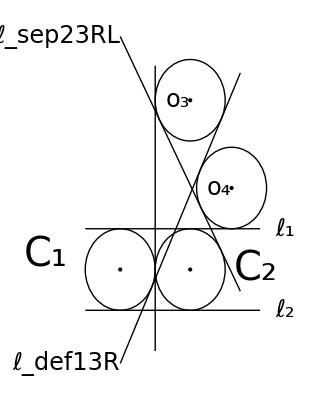

```mathematica
(*taken from: CriticalFamiliesSize4Overlapping *)(*Compare with Case A(i)*)
δ=r;
 (*magnitude of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;

ℓsep23Slope=-Sqrt[y3^2-4 r^2]/(2r);(*slope of line lsep for C2/C3*)
ℓsep23int=ℓsep23Slope*(-r)+y3/2;
ℓdef13RSlope=y3/(2r);(*slope of line lsep for C2/C3*)
ℓdef13Rint=(-Sqrt[y3^2+4 r^2]+y3)/2;
t=(2/3)r + δ; (*t must be in the bound δ+2r < t < 3δ *)(*center x-  coordinate for C3*)
γ=r;(*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
y3=4.152865293655491;
Subscript[x, 4]=(2r)/y3(Sqrt[y3^2+4 r^2]+2r-y3/2);(*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
y4=2r
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{-r-r,r},{γ+2r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{-r-r,-r},{γ+2r,-r}}],Black,(*support line Subscript[ℓ, v], vertical*)Line[{{0,-(2r)},{0,(5r)}}]}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r/2,r/3},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+2r+b/2,-2r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def13R]*)Line[{{-r,ℓdef13RSlope*(-r)+ℓdef13Rint},{Subscript[x, 4]+r/4,ℓdef13RSlope*(Subscript[x, 4]+r/4)+ℓdef13Rint}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep23]*)Line[{{-r,ℓsep23Slope*(-r)+ℓsep23int},{Subscript[x, 4]+r/4,ℓsep23Slope*(Subscript[x, 4]+r/4)+ℓsep23int}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, def13R],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-r,ℓdef13RSlope*(-r)+ℓdef13Rint},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, sep23RL],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-r,ℓsep23Slope*(-r)+ℓsep23int},{1,0}]];
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,y3}],Point[{Subscript[x, 4],y4}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,y3},r],(*Disk C4 *)Circle[{Subscript[x, 4],y4},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,y3},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],y4},{1,0}]];
g22=Graphics[Text[
Style[Subscript[ℓ, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{4r,r},{1,0}]];
g23=Graphics[Text[
Style[Subscript[ℓ, 2],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{4r,-r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentvii *)(*see handwritten pages for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21,g22,g23]
```

#### Solve for y3

The following equation contains  the two expressions for the slope of ellsep23

```mathematica
Clear[r,y3,γ]
PowerExpand[MultiplySides[(y3(2r-y3))/(2r(Sqrt[y3^2+4 r^2]+2r-y3/2)-γ*y3)==(-Sqrt[y3^2-4 r^2])/(2r),2r(2r(Sqrt[y3^2+4 r^2]+2r-y3/2)-γ*y3)]]
```

Piecewise[{{2 r (2 r-y3) y3==-√(-4 r^2+y3^2) (2 r (2 r-y3/2+√(4 r^2+y3^2))-y3 γ), 2 r (2 r (2 r-y3/2+√(4 r^2+y3^2))-y3 γ)≠0}, {((2 r-y3) y3)/(2 r (2 r-y3/2+√(4 r^2+y3^2))-y3 γ)==-(√(-4 r^2+y3^2))/(2 r), True}}]

```mathematica
Expand[(2 r (2 r-y3) y3)^2==(-√(-4 r^2+y3^2) (2 r (2 r-y3/2+√(4 r^2+y3^2))-y3 γ))^2]
```

16 r^4 y3^2-16 r^3 y3^3+4 r^2 y3^4==-128 r^6+32 r^5 y3+12 r^4 y3^2-8 r^3 y3^3+5 r^2 y3^4-64 r^5 √(4 r^2+y3^2)+16 r^4 y3 √(4 r^2+y3^2)+16 r^3 y3^2 √(4 r^2+y3^2)-4 r^2 y3^3 √(4 r^2+y3^2)+32 r^4 y3 γ-8 r^3 y3^2 γ-8 r^2 y3^3 γ+2 r y3^4 γ+16 r^3 y3 √(4 r^2+y3^2) γ-4 r y3^3 √(4 r^2+y3^2) γ-4 r^2 y3^2 γ^2+y3^4 γ^2

```mathematica
Collect[16 r^4 y3^2-16 r^3 y3^3+4 r^2 y3^4==-128 r^6+32 r^5 y3+12 r^4 y3^2-8 r^3 y3^3+5 r^2 y3^4-64 r^5 √(4 r^2+y3^2)+16 r^4 y3 √(4 r^2+y3^2)+16 r^3 y3^2 √(4 r^2+y3^2)-4 r^2 y3^3 √(4 r^2+y3^2)+32 r^4 y3 γ-8 r^3 y3^2 γ-8 r^2 y3^3 γ+2 r y3^4 γ+16 r^3 y3 √(4 r^2+y3^2) γ-4 r y3^3 √(4 r^2+y3^2) γ-4 r^2 y3^2 γ^2+y3^4 γ^2,√(4 r^2+y3^2)]
```

16 r^4 y3^2-16 r^3 y3^3+4 r^2 y3^4==-128 r^6+32 r^5 y3+12 r^4 y3^2-8 r^3 y3^3+5 r^2 y3^4+32 r^4 y3 γ-8 r^3 y3^2 γ-8 r^2 y3^3 γ+2 r y3^4 γ-4 r^2 y3^2 γ^2+y3^4 γ^2+√(4 r^2+y3^2) (-64 r^5+16 r^4 y3+16 r^3 y3^2-4 r^2 y3^3+16 r^3 y3 γ-4 r y3^3 γ)

```mathematica
AddSides[16 r^4 y3^2-16 r^3 y3^3+4 r^2 y3^4==-128 r^6+32 r^5 y3+12 r^4 y3^2-8 r^3 y3^3+5 r^2 y3^4+32 r^4 y3 γ-8 r^3 y3^2 γ-8 r^2 y3^3 γ+2 r y3^4 γ-4 r^2 y3^2 γ^2+y3^4 γ^2+√(4 r^2+y3^2) (-64 r^5+16 r^4 y3+16 r^3 y3^2-4 r^2 y3^3+16 r^3 y3 γ-4 r y3^3 γ),-(-128 r^6+32 r^5 y3+12 r^4 y3^2-8 r^3 y3^3+5 r^2 y3^4+32 r^4 y3 γ-8 r^3 y3^2 γ-8 r^2 y3^3 γ+2 r y3^4 γ-4 r^2 y3^2 γ^2+y3^4 γ^2)]
```

128 r^6-32 r^5 y3+4 r^4 y3^2-8 r^3 y3^3-r^2 y3^4-32 r^4 y3 γ+8 r^3 y3^2 γ+8 r^2 y3^3 γ-2 r y3^4 γ+4 r^2 y3^2 γ^2-y3^4 γ^2==√(4 r^2+y3^2) (-64 r^5+16 r^4 y3+16 r^3 y3^2-4 r^2 y3^3+16 r^3 y3 γ-4 r y3^3 γ)

```mathematica
Expand[(128 r^6-32 r^5 y3+4 r^4 y3^2-8 r^3 y3^3-r^2 y3^4-32 r^4 y3 γ+8 r^3 y3^2 γ+8 r^2 y3^3 γ-2 r y3^4 γ+4 r^2 y3^2 γ^2-y3^4 γ^2)^2==(√(4 r^2+y3^2) (-64 r^5+16 r^4 y3+16 r^3 y3^2-4 r^2 y3^3+16 r^3 y3 γ-4 r y3^3 γ))^2]
```

16384 r^12-8192 r^11 y3+2048 r^10 y3^2-2304 r^9 y3^3+272 r^8 y3^4+56 r^6 y3^6+16 r^5 y3^7+r^4 y3^8-8192 r^10 y3 γ+4096 r^9 y3^2 γ+1280 r^8 y3^3 γ-448 r^7 y3^4 γ+128 r^6 y3^5 γ-160 r^5 y3^6 γ+16 r^4 y3^7 γ+4 r^3 y3^8 γ+2048 r^8 y3^2 γ^2-768 r^7 y3^3 γ^2-672 r^6 y3^4 γ^2+256 r^5 y3^5 γ^2+16 r^4 y3^6 γ^2-16 r^3 y3^7 γ^2+6 r^2 y3^8 γ^2-256 r^6 y3^3 γ^3+64 r^5 y3^4 γ^3+128 r^4 y3^5 γ^3-32 r^3 y3^6 γ^3-16 r^2 y3^7 γ^3+4 r y3^8 γ^3+16 r^4 y3^4 γ^4-8 r^2 y3^6 γ^4+y3^8 γ^4==16384 r^12-8192 r^11 y3-3072 r^10 y3^2+2048 r^9 y3^3-1280 r^8 y3^4+512 r^7 y3^5+192 r^6 y3^6-128 r^5 y3^7+16 r^4 y3^8-8192 r^10 y3 γ+2048 r^9 y3^2 γ+2048 r^8 y3^3 γ-512 r^7 y3^4 γ+512 r^6 y3^5 γ-128 r^5 y3^6 γ-128 r^4 y3^7 γ+32 r^3 y3^8 γ+1024 r^8 y3^2 γ^2-256 r^6 y3^4 γ^2-64 r^4 y3^6 γ^2+16 r^2 y3^8 γ^2

Combine it all

```mathematica
AddSides[16384 r^12-8192 r^11 y3+2048 r^10 y3^2-2304 r^9 y3^3+272 r^8 y3^4+56 r^6 y3^6+16 r^5 y3^7+r^4 y3^8-8192 r^10 y3 γ+4096 r^9 y3^2 γ+1280 r^8 y3^3 γ-448 r^7 y3^4 γ+128 r^6 y3^5 γ-160 r^5 y3^6 γ+16 r^4 y3^7 γ+4 r^3 y3^8 γ+2048 r^8 y3^2 γ^2-768 r^7 y3^3 γ^2-672 r^6 y3^4 γ^2+256 r^5 y3^5 γ^2+16 r^4 y3^6 γ^2-16 r^3 y3^7 γ^2+6 r^2 y3^8 γ^2-256 r^6 y3^3 γ^3+64 r^5 y3^4 γ^3+128 r^4 y3^5 γ^3-32 r^3 y3^6 γ^3-16 r^2 y3^7 γ^3+4 r y3^8 γ^3+16 r^4 y3^4 γ^4-8 r^2 y3^6 γ^4+y3^8 γ^4==16384 r^12-8192 r^11 y3-3072 r^10 y3^2+2048 r^9 y3^3-1280 r^8 y3^4+512 r^7 y3^5+192 r^6 y3^6-128 r^5 y3^7+16 r^4 y3^8-8192 r^10 y3 γ+2048 r^9 y3^2 γ+2048 r^8 y3^3 γ-512 r^7 y3^4 γ+512 r^6 y3^5 γ-128 r^5 y3^6 γ-128 r^4 y3^7 γ+32 r^3 y3^8 γ+1024 r^8 y3^2 γ^2-256 r^6 y3^4 γ^2-64 r^4 y3^6 γ^2+16 r^2 y3^8 γ^2,-(16384 r^12-8192 r^11 y3-3072 r^10 y3^2+2048 r^9 y3^3-1280 r^8 y3^4+512 r^7 y3^5+192 r^6 y3^6-128 r^5 y3^7+16 r^4 y3^8-8192 r^10 y3 γ+2048 r^9 y3^2 γ+2048 r^8 y3^3 γ-512 r^7 y3^4 γ+512 r^6 y3^5 γ-128 r^5 y3^6 γ-128 r^4 y3^7 γ+32 r^3 y3^8 γ+1024 r^8 y3^2 γ^2-256 r^6 y3^4 γ^2-64 r^4 y3^6 γ^2+16 r^2 y3^8 γ^2)]
```

5120 r^10 y3^2-4352 r^9 y3^3+1552 r^8 y3^4-512 r^7 y3^5-136 r^6 y3^6+144 r^5 y3^7-15 r^4 y3^8+2048 r^9 y3^2 γ-768 r^8 y3^3 γ+64 r^7 y3^4 γ-384 r^6 y3^5 γ-32 r^5 y3^6 γ+144 r^4 y3^7 γ-28 r^3 y3^8 γ+1024 r^8 y3^2 γ^2-768 r^7 y3^3 γ^2-416 r^6 y3^4 γ^2+256 r^5 y3^5 γ^2+80 r^4 y3^6 γ^2-16 r^3 y3^7 γ^2-10 r^2 y3^8 γ^2-256 r^6 y3^3 γ^3+64 r^5 y3^4 γ^3+128 r^4 y3^5 γ^3-32 r^3 y3^6 γ^3-16 r^2 y3^7 γ^3+4 r y3^8 γ^3+16 r^4 y3^4 γ^4-8 r^2 y3^6 γ^4+y3^8 γ^4==0

```mathematica
Collect[5120 r^10 y3^2-4352 r^9 y3^3+1552 r^8 y3^4-512 r^7 y3^5-136 r^6 y3^6+144 r^5 y3^7-15 r^4 y3^8+2048 r^9 y3^2 γ-768 r^8 y3^3 γ+64 r^7 y3^4 γ-384 r^6 y3^5 γ-32 r^5 y3^6 γ+144 r^4 y3^7 γ-28 r^3 y3^8 γ+1024 r^8 y3^2 γ^2-768 r^7 y3^3 γ^2-416 r^6 y3^4 γ^2+256 r^5 y3^5 γ^2+80 r^4 y3^6 γ^2-16 r^3 y3^7 γ^2-10 r^2 y3^8 γ^2-256 r^6 y3^3 γ^3+64 r^5 y3^4 γ^3+128 r^4 y3^5 γ^3-32 r^3 y3^6 γ^3-16 r^2 y3^7 γ^3+4 r y3^8 γ^3+16 r^4 y3^4 γ^4-8 r^2 y3^6 γ^4+y3^8 γ^4==0,y3]
```

y3^2 (5120 r^10+2048 r^9 γ+1024 r^8 γ^2)+y3^7 (144 r^5+144 r^4 γ-16 r^3 γ^2-16 r^2 γ^3)+y3^5 (-512 r^7-384 r^6 γ+256 r^5 γ^2+128 r^4 γ^3)+y3^3 (-4352 r^9-768 r^8 γ-768 r^7 γ^2-256 r^6 γ^3)+y3^8 (-15 r^4-28 r^3 γ-10 r^2 γ^2+4 r γ^3+γ^4)+y3^6 (-136 r^6-32 r^5 γ+80 r^4 γ^2-32 r^3 γ^3-8 r^2 γ^4)+y3^4 (1552 r^8+64 r^7 γ-416 r^6 γ^2+64 r^5 γ^3+16 r^4 γ^4)==0

```mathematica
Clear[r,γ,y3]
y3^2 (5120 r^10+2048 r^9 γ+1024 r^8 γ^2)+y3^7 (144 r^5+144 r^4 γ-16 r^3 γ^2-16 r^2 γ^3)+y3^5 (-512 r^7-384 r^6 γ+256 r^5 γ^2+128 r^4 γ^3)+y3^3 (-4352 r^9-768 r^8 γ-768 r^7 γ^2-256 r^6 γ^3)+y3^8 (-15 r^4-28 r^3 γ-10 r^2 γ^2+4 r γ^3+γ^4)+y3^6 (-136 r^6-32 r^5 γ+80 r^4 γ^2-32 r^3 γ^3-8 r^2 γ^4)+y3^4 (1552 r^8+64 r^7 γ-416 r^6 γ^2+64 r^5 γ^3+16 r^4 γ^4)/.γ->r
```

8192 r^10 y3^2-6144 r^9 y3^3+1280 r^8 y3^4-512 r^7 y3^5-128 r^6 y3^6+256 r^5 y3^7-48 r^4 y3^8

```mathematica
-(8192 r^10 y3^2-6144 r^9 y3^3+1280 r^8 y3^4-512 r^7 y3^5-128 r^6 y3^6+256 r^5 y3^7-48 r^4 y3^8)
```

-8192 r^10 y3^2+6144 r^9 y3^3-1280 r^8 y3^4+512 r^7 y3^5+128 r^6 y3^6-256 r^5 y3^7+48 r^4 y3^8

```mathematica
Clear[r,y3]
r=1;
NSolve[8192 r^10 y3^2-6144 r^9 y3^3+1280 r^8 y3^4-512 r^7 y3^5-128 r^6 y3^6+256 r^5 y3^7-48 r^4 y3^8==0,y3]
```

{{y3→-2.46485},{y3→-0.177343-2.03391 ⅈ},{y3→-0.177343+2.03391 ⅈ},{y3→0.},{y3→0.},{y3→2.},{y3→2.},{y3→4.15287}}

```mathematica
Clear[r,y3]
(*r=1;*)
Solve[8192 r^10 y3^2-6144 r^9 y3^3+1280 r^8 y3^4-512 r^7 y3^5-128 r^6 y3^6+256 r^5 y3^7-48 r^4 y3^8==0,y3](*The solutions are not easily expressible*)
```

{{y3→0},{y3→0},{y3→2 r},{y3→2 r},{y3→r/3-1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))-1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→r/3-1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))-1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))}}

Rewrite the equation

```mathematica
Clear[r,y3]
Factor[8192 r^10 y3^2-6144 r^9 y3^3+1280 r^8 y3^4-512 r^7 y3^5-128 r^6 y3^6+256 r^5 y3^7-48 r^4 y3^8]
```

16 r^4 (2 r-y3)^2 y3^2 (128 r^4+32 r^3 y3+20 r^2 y3^2+4 r y3^3-3 y3^4)

```mathematica
Cancel[(8192 r^10 y3^2-6144 r^9 y3^3+1280 r^8 y3^4-512 r^7 y3^5-128 r^6 y3^6+256 r^5 y3^7-48 r^4 y3^8)/(-16*r^4*y3^2)]
```

-512 r^6+384 r^5 y3-80 r^4 y3^2+32 r^3 y3^3+8 r^2 y3^4-16 r y3^5+3 y3^6

```mathematica
Factor[-512 r^6+384 r^5 y3-80 r^4 y3^2+32 r^3 y3^3+8 r^2 y3^4-16 r y3^5+3 y3^6]
```

-(2 r-y3)^2 (128 r^4+32 r^3 y3+20 r^2 y3^2+4 r y3^3-3 y3^4)

```mathematica
Clear[r,y3]
(*r=1*)
Solve[128 r^4+32 r^3 y3+20 r^2 y3^2+4 r y3^3-3 y3^4==0,y3]
```

{{y3→r/3-1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))-1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→r/3-1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)-(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))-1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))},{y3→r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))}}

```mathematica
r=1
N[r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))]
```

1

4.15287+2.22045×10^-16 ⅈ

This is the solution, rewrite it

```mathematica
Clear[r]
r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 (-4049 r^6-192 √1086 r^6)^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+(-4049 r^6-192 √1086 r^6)^(1/3))))
```

```mathematica
r/3+1/3 √(11 r^2-(287 r^4)/((-4049 r^6-192 √1086 r^6)^(1/3))+r^2*(-4049 -192 √1086 )^(1/3))+1/2 √((88 r^2)/9+(1148 r^4)/(9 (-4049 r^6-192 √1086 r^6)^(1/3))-4/9 *r^2*(-4049 -192 √1086 )^(1/3)+(416 r^3)/(9 √(11 r^2-(287 r^4)/(r^2(-4049 -192 √1086 )^(1/3))+r^2*(-4049 -192 √1086)^(1/3))))
```

```mathematica
r/3+r/3 √(11 -(287 r^2)/(r^2(-4049 -192 √1086)^(1/3))+(-4049 -192 √1086 )^(1/3))+r/2 √(88/9+(1148 r^2)/(9 r^2(-4049 -192 √1086 )^(1/3))-4/9 *(-4049 -192 √1086 )^(1/3)+(416 r)/(9 *r*√(11 -(287 r^2)/(r^2(-4049 -192 √1086 )^(1/3))+(-4049 -192 √1086)^(1/3))))
```

```mathematica
r/3+r/3 √(11 +287/(4049 +192 √1086 )^(1/3)-(4049 +192 √1086 )^(1/3))+r/2 √(88/9-1148/(9 (4049 +192 √1086 )^(1/3))+4/9 *(4049 +192 √1086 )^(1/3)+416/(9 *√(11 +287/(4049 +192 √1086 )^(1/3)-(4049 +192 √1086)^(1/3))))
```

Can the expression directly above be improved to a useable expression? Or the one directly below?(1/11/21)

```mathematica
α= (4049 +192 √1086 )^(1/3)
r/3+r/3 √(11 +287/α-α)+r/2 √(88/9-1148/(9 α)+4/9 *α+416/(9 *√(11 +287/α-α)))
```

```mathematica
α= (4049 +192 √1086 )^(1/3)
r=1
N[r/3+r/3 √(11 +287/α-α)+r/6 √(88 -1148/α+4 *α+416/(√(11 +287/α-α)))]
```

```mathematica
α= (4049 +192 √1086 )^(1/3)
r=1
N[r/3(1+ √(11 +287/α-α)+1/2 √(88 -1148/α+4 *α+416/(√(11 +287/α-α))))]
```

```mathematica
α= (4049 +192 √1086 )^(1/3)
β=√(11 +287/α-α)
r=1
N[r/3(1+ β+1/2 √(88 -1148/α+4 *α+416/β))]
```

## Tangent Critical F4, case (viii) , ℓ_def13R supports C4 on LHS, ℓ_def23R supports C4 on left

2

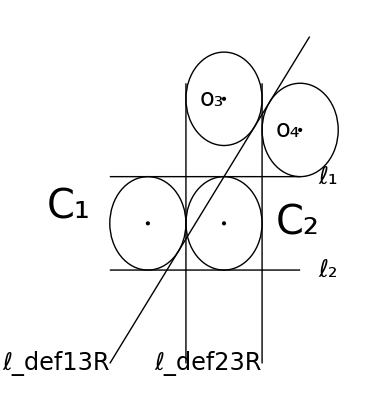

```mathematica
(*taken from: CriticalFamiliesSize4Overlapping *)(*Compare with Case A(i)*)
δ=r;
 (*magnitude of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;
ℓdef13RSlope=4/3;(*slope of line lsep for C2/C3*)
ℓdef13Rint=-r/3;
t=(2/3)r + δ; (*t must be in the bound δ+2r < t < 3δ *)(*center x-  coordinate for C3*)
γ=r;(*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
y3=8/3 r;
Subscript[x, 4]=3r;(*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
y4=2r
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{-r-r,r},{γ+2r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{-r-r,-r},{γ+2r,-r}}],Black,(*support line Subscript[ℓ, v], vertical*)Line[{{0,-(3r)},{0,(3r)}}]}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r/2,r/3},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+2r+b/2,-2r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def13R]*)Line[{{-2r,ℓdef13RSlope*(-2r)+ℓdef13Rint},{Subscript[x, 4]+r/4,ℓdef13RSlope*(Subscript[x, 4]+r/4)+ℓdef13Rint}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep23R], vertical*)Line[{{γ+r,-3r},{γ+r,3r}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, def13R],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2r,ℓdef13RSlope*(-2r)+ℓdef13Rint},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, def23R],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ+r,-3r},{1,0}]];
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,y3}],Point[{Subscript[x, 4],y4}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,y3},r],(*Disk C4 *)Circle[{Subscript[x, 4],y4},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,y3},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],y4},{1,0}]];
g22=Graphics[Text[
Style[Subscript[ℓ, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{4r,r},{1,0}]];
g23=Graphics[Text[
Style[Subscript[ℓ, 2],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{4r,-r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentviii *)(*see handwritten pages for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21,g22,g23]
```

## Tangent Critical F4, page 6 1/2 initial assessment, first case (ix), x4<0, ℓ_sep13 supports C4 on RHS, ℓ_sep23 supports C4 on right

2

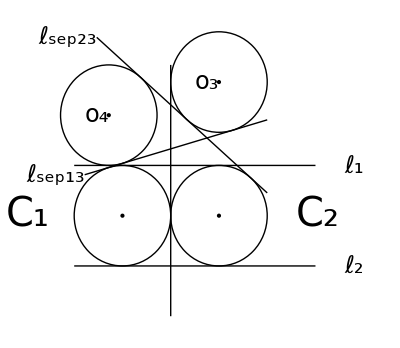

```mathematica
(*taken from: CriticalFamiliesSize4Overlapping *)(*Compare with Case A(i)*)
δ=r;
 (*magnitude of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;
ℓsep13Slope=(y3^2-4 r^2)/(4r*y3);(*slope of line lsep for C2/C3*)
ℓsep13int=y3/2;
t=(2/3)r + δ; (*t must be in the bound δ+2r < t < 3δ *)(*center x-  coordinate for C3*)
γ=r;(*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
y3=2.658967081916994;
Subscript[x, 4]=(r (4 r^2-8 r y3+3 y3^2))/(4 r^2-y3^2);(*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
ℓsep23Slope=(-Sqrt[y3^2-4 r^2])/(2r);
ℓsep23int=ℓsep23Slope*(-r)+y3/2;
y4=2r
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{-r-r,r},{γ+2r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{-r-r,-r},{γ+2r,-r}}],Black,(*support line Subscript[ℓ, v], vertical*)Line[{{0,-(2r)},{0,(3r)}}]}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r/2,0},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+2r+b/2,-2r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, sep13]*)Line[{{Subscript[x, 4]-r/2,ℓsep13Slope*(Subscript[x, 4]-r/2)+ℓsep13int},{2r,ℓsep13Slope*(2r)+ℓsep13int}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep23]*)Line[{{Subscript[x, 4]-r/4,ℓsep23Slope*(Subscript[x, 4]-r/4)+ℓsep23int},{2r,ℓsep23Slope*(2r)+ℓsep23int}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, sep13],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]-r/2,ℓsep13Slope*(Subscript[x, 4]-r/2)+ℓsep13int},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, sep23],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]-r/4,ℓsep23Slope*(Subscript[x, 4]-r/4)+ℓsep23int},{1,0}]];
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,y3}],Point[{Subscript[x, 4],y4}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,y3},r],(*Disk C4 *)Circle[{Subscript[x, 4],y4},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,y3},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],y4},{1,0}]];
g22=Graphics[Text[
Style[Subscript[ℓ, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{4r,r},{1,0}]];
g23=Graphics[Text[
Style[Subscript[ℓ, 2],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{4r,-r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentix *)(*see handwritten pages for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21,g22,g23]
```

```mathematica
x4=(4*r*y3)/(y3^2-4 r^2)*((-Sqrt[(y3^2-4 r^2)^2+16 r^2*y3^2])/(4y3)+2r-y3/2)
```

```mathematica
Simplify[(4*r*y3)/(y3^2-4 r^2)*((-Sqrt[(y3^2-4 r^2)^2+16 r^2*y3^2])/(4y3)+2r-y3/2)]
```

(r (-8 r y3+2 y3^2+√((4 r^2+y3^2)^2)))/(4 r^2-y3^2)

```mathematica
PowerExpand[(r (-8 r y3+2 y3^2+√((4 r^2+y3^2)^2)))/(4 r^2-y3^2)]
```

(r (4 r^2-8 r y3+3 y3^2))/(4 r^2-y3^2)

#### Calculating y3

the equation relates two expressions for slope of ellsep23

```mathematica
Clear[r,y3]
Simplify[(2r)/(r-(r (4 r^2-8 r y3+3 y3^2))/(4 r^2-y3^2))==-Sqrt[y3^2-4 r^2]/(2r)]
```

1+(2 r)/y3+(√(-4 r^2+y3^2))/r==0

```mathematica
AddSides[1+(2 r)/y3+(√(-4 r^2+y3^2))/r==0,-(√(-4 r^2+y3^2))/r]
```

1+(2 r)/y3==-(√(-4 r^2+y3^2))/r

```mathematica
Expand[(1+(2 r)/y3)^2==(-(√(-4 r^2+y3^2))/r)^2]
```

1+(4 r^2)/y3^2+(4 r)/y3==-4+y3^2/r^2

```mathematica
ExpandAll[MultiplySides[1+(4 r^2)/y3^2+(4 r)/y3==-4+y3^2/r^2,r^2*y3^2]]
```

Piecewise[{{1+(4 r^2)/y3^2+(4 r)/y3==-4+y3^2/r^2, r^2 y3^2==0}, {4 r^4+4 r^3 y3+r^2 y3^2==-4 r^2 y3^2+y3^4, True}}]

```mathematica
AddSides[4 r^4+4 r^3 y3+r^2 y3^2==-4 r^2 y3^2+y3^4,-(-4 r^2 y3^2+y3^4)]
```

4 r^4+4 r^3 y3+5 r^2 y3^2-y3^4==0

```mathematica
Clear[r,y3]
r=1
NSolve[4 r^4+4 r^3 y3+5 r^2 y3^2-y3^4==0,y3]
```

1

{{y3→-2.},{y3→-0.329484-0.802255 ⅈ},{y3→-0.329484+0.802255 ⅈ},{y3→2.65897}}

## Tangent Critical F4, p.6 1/2 of Initial Assessment second case (x) , ℓ_sep13 supports C4 on LHS, ℓ_def23R supports C4 on left

2

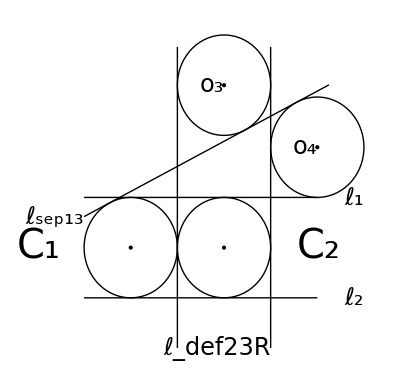

```mathematica
(*taken from: CriticalFamiliesSize4Overlapping *)(*Compare with Case A(i)*)
δ=r;
 (*magnitude of x-coordinate of center of disk Subscript[C, 1] and Subscript[C, 2]*)
r=1; (*common radius of disk Subscript[C, 1] and Subscript[C, 2]*)
ε=δ/5;
ℓsep13Slope=(y3^2-4 r^2)/(4r*y3);(*slope of line lsep for C2/C3*)
ℓsep13int=y3/2;
t=(2/3)r + δ; (*t must be in the bound δ+2r < t < 3δ *)(*center x-  coordinate for C3*)
γ=r;(*γ is x-coordinate of center of disk Subscript[C, 3]*)(*We use the absolute value for γ*)
y3=r(1+Sqrt[5]);
Subscript[x, 4]=3r;(*Subscript[x, 4] is x-coordinate of center of disk Subscript[C, 4]*)(*We are not using the absolute value for Subscript[x, 4]*)
y4=2r
b=r/(2δ);(*a small buffer term*)
ycoordcirclab=-r/2;
labelfontsize=40;
centerlabelfontsize=24;
g1=Graphics[{(*Disk Subscript[C, 1]*)Circle[{-δ,0},r],(*Disk Subscript[C, 2]*)Circle[{δ,0},r](*,(*Disk Subscript[C, 3]*)Circle[{t,0},r]*)}(*,Axes->True,Ticks->None,AxesLabel->{x,y}*)];
g2=Graphics[{Black,(*horizontal line Subscript[ℓ, 1]*)Line[{{-r-r,r},{γ+2r,r}}],Black,(*horizontal line Subscript[ℓ, 2]*)Line[{{-r-r,-r},{γ+2r,-r}}],Black,(*support line Subscript[ℓ, v], vertical*)Line[{{0,-(2r)},{0,(4r)}}]}];
g3=Graphics[Text[
StyleForm[Subscript[C, 1],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-δ-r-r/2,0},{1,0}]];
(*g4=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+b/2,2ycoordcirclab-b/2},{1,0}]];*)
g7=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{δ+r+r+r/2,0},{1,0}]];
(*g9=Graphics[Text[
StyleForm[Subscript[C, 4],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4]+2r+b/2,-2r},{1,0}]];*)
g12=Graphics[{Black,(* support line Subscript[ℓ, def13R]*)Line[{{-2r,ℓsep13Slope*(-2r)+ℓsep13int},{Subscript[x, 4]+r/4,ℓsep13Slope*(Subscript[x, 4]+r/4)+ℓsep13int}}] }];
g13=Graphics[{Black,(* support line Subscript[ℓ, sep23R], vertical*)Line[{{γ+r,-2r},{γ+r,4r}}] }];

(*g14=Graphics[Text[
Style[Subscript[m, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2δ,3r},{1,0}]];*)
g15=Graphics[Text[
Style[Subscript[ℓ, sep13],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{-2r,ℓsep13Slope*(-2r)+ℓsep13int},{1,0}]];
g16=Graphics[Text[
Style[Subscript[ℓ, def23R],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ+r,-2r},{1,0}]];
g17=Graphics[{Point[{-δ,-0}],Point[{δ,0}],(*Point[{t,0}],*)Point[{γ,y3}],Point[{Subscript[x, 4],y4}],PointSize[0.05]}];
g18=Graphics[{(*Green,*)(*Disk C3*)Circle[{γ,y3},r],(*Disk C4 *)Circle[{Subscript[x, 4],y4},r]}];
(*g19=Graphics[Text[
StyleForm[Subscript[C, 2],FontSize ->labelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{r,2r+r/2},{1,0}]];*)
g20=Graphics[Text[
Style[Subscript[o, 3],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{γ,y3},{1,0}]];
g21=Graphics[Text[
Style[Subscript[o, 4],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{Subscript[x, 4],y4},{1,0}]];
g22=Graphics[Text[
Style[Subscript[ℓ, 1],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{4r,r},{1,0}]];
g23=Graphics[Text[
Style[Subscript[ℓ, 2],FontSize ->centerlabelfontsize,FontWeight ->"Thin",FontFamily->"Courier New"],{4r,-r},{1,0}]];

(* Label: CriticalFamiliesSize4Tangentx *)(*see handwritten pages for this labeling scheme *)

Show[g1,g2,g3,(*g4,*)(*g5,g6,*)g7(*g8*),(*g9,*)(*g10,*)(*g11,*)g12,g13,(*g14,*)g15,g16,g17,g18,(*g19,*)g20,g21,g22,g23]
```